# How to Grade Predictions

## Problem Statement

Every morning, two weathermen each state a probability of rain. Every day, either it rains or it doesn’t. How can we tell which weatherman is better?
(More generally, if somebody makes a bunch of predictions, like “I’m 80% confident Syria’s civil war won’t end in 2015,” how do you tell “how good” that person is at predicting things? But for now, let’s just talk in terms of weathermen.)

## “Surprise” as a grading metric

It'd be great if we could take a list of prediction-probabilities (one weatherman's estimated probabilities), and a list of outcomes (whether it actually rained each day), and come up with a score saying how good the predictions were. Let's call this score the "surprise." Like golf, a small number is better: good predictions will result in a small surprise, and bad predictions in a large surprise.

What are some features that "surprise" must have?
- The best possible set of predictions ("100%" for days it rains, and "0%" for days it doesn't) should have the smallest possible surprise.
- The worst possible set of predictions ("0%" for days it rains, "100%" for days it doesn't) should have the smallest possible surprise.
- All other sets of predictions should have surprises strictly between those two surprises.
- Surprise should be "symmetric," in some sense: saying "70%" and seeing rain should be just as surprising as saying "30%" and seeing not-rain.

What are some features we want "surprise" to have?
- The surprise associated with multiple predictions should be the sums of the surprises of the individual predictions.

How about this definition?

```mathematica
Clear[surprise]
surprise[p_?(0≤#≤1&),happened_]:=-Log[If[happened,p,1-p]]
surprise[ps_List,happened_List]:=Total[MapThread[surprise,{ps,happened}]]/;Length[happened]==Length[ps]
```

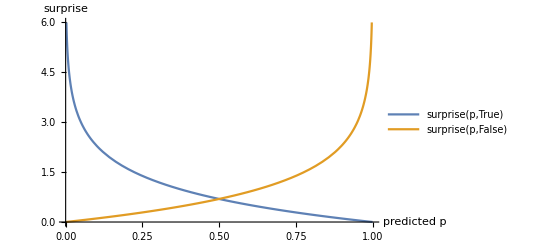

```mathematica
Plot[
{surprise[p,True],surprise[p,False]},
{p,0,1},
PlotRange->{All,{0,6}},
PlotLegends->"Expressions",
AxesLabel->{"predicted p","surprise"}]
```

```mathematica
On[Assert]
Assert[surprise[1,True]==0]
Assert[surprise[1,False]==∞]
halfSurprise=surprise[1/2,True];
Assert[
surprise[{1/2,1/2,1/2,1/2},{False,False,False,False}]==
surprise[{1/2,1/2,1/2,1/2},{False,False,True,True}]==
surprise[{1/2,1/2,1/2,1/2},{True,True,True,True}]==
4*halfSurprise];
Off[Assert]
```

### Expected surprise

If you predict rain with probability p, how surprised should you expect to be? i.e. what’s the expected value of the surprise?
(If our definition of “surprise” is good, intuitively I think we should get very low expected surprise if p is close to 0 or 1, since then the outcome is almost certain to be unsurprising.)
Well, with probability p the surprise will be surprise(p,True).
And with probability 1-p, the surprise will be surprise(p,False).
So the expected surprise will be p·surprise(p,True) + (1-p)·surprise(p,False).
Let’s plot that.

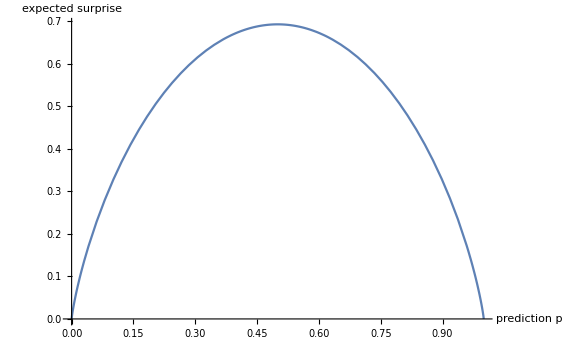

```mathematica
Plot[p surprise[p,True]+(1-p)surprise[p,False],{p,0,1},AxesLabel->{"prediction p","expected surprise"}]
```

LOOK FAMILIAR?
Yes, that’s exactly what you think it is.
I think this is a sign that we're doing something right.

## Surprise p-values

A natural question is: “Is it possible that rain truly is literally unpredictable, and this weatherman is doing literally as well as any non-magical weatherman can?”
i.e. “Can we reject the hypothesis that this weatherman is as good as possible?”
i.e. “If this weatherman is as good as possible, if he made these predictions, what fraction of the time would we expect the mean-surprise to be this high?”

First, we need to be able to generate data consistent with the null hypothesis:

```mathematica
Clear[randomObservation]
randomObservation[predictionP_]:=(RandomVariate[BernoulliDistribution[predictionP]]==1)
SetAttributes[randomObservation,Listable]
Print[
{Count[randomObservation[Table[0,{1000}]],True],
Count[randomObservation[Table[0.3,{1000}]],True],
Count[randomObservation[Table[1,{1000}]],True],
Count[randomObservation[Table[i/1000,{i,1000}]],True]},
" should be {0, [about 300], 1000, [about 500]}"
]
```

{0,309,1000,493} should be {0, [about 300], 1000, [about 500]}

Now, a brute-force way to calculate a p-value: generate a zillion piles of data consistent with the null hypothesis, and see how often the surprise is as high as the true surprise.

```mathematica
Clear[randomSurprises,pValue]
randomSurprises[predictions_List,n_Integer]:=surprise[predictions,#]&/@Table[randomObservation[predictions],{n}]
pValue[predictions_List,observations_List]:=Module[
{nTrials,trueSurprise,nhObservationSets,nhSurprises},
nTrials=1000;
trueSurprise=surprise[predictions,observations];
nhSurprises=randomSurprises[predictions,nTrials];
Length[Select[nhSurprises,#≥trueSurprise&]]/nTrials
]
```

```mathematica
Table[pValue[Table[.8,{3}],Table[False,{3}]],{10}]//N
```

{0.006,0.004,0.01,0.007,0.012,0.008,0.005,0.004,0.006,0.007}

Just to make sure we coded pValue correctly, let’s generate p-values for a bunch of datasets where the null hypothesis is true, and make sure they’re uniformly distributed between 0 and 1.

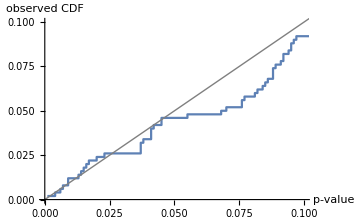
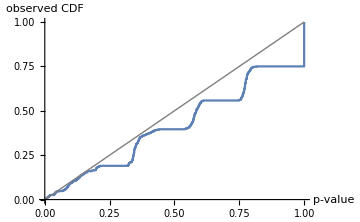

```mathematica
Module[
{nPoints:=500,ps:={.1,.2,.3,.5,.7,.8,.8},observationSets,pValues},
observationSets=Table[randomObservation[ps],{nPoints}];
pValues=Sort[pValue[ps,#]&/@observationSets];
Row[{
ListStepPlot[
Table[{pValues⟦i⟧,i/nPoints},{i,nPoints}],
Epilog->{Gray,Line[{{0,0},{1,1}}]},
AxesLabel->{"p-value","observed CDF"},
PlotRange->{{0,0.1},{0,0.1}},
ImageSize->Medium],
ListStepPlot[
Table[{pValues⟦i⟧,i/nPoints},{i,nPoints}],
Epilog->{Gray,Line[{{0,0},{1,1}}]},
AxesLabel->{"p-value","observed CDF"},
ImageSize->Medium]
}]]
```

Is that deviation okay? I don’t know. I suspect it’s not too bad, but I don’t have much to back that assertion up.

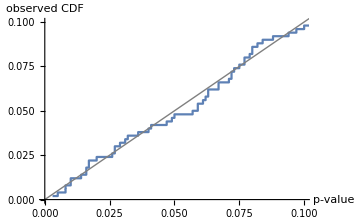
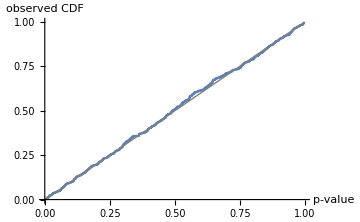
-Graphics--Graphics-[681]

```mathematica
%[681]
```

## Evaluation of Scott Alexander’s 2015 predictions

Predictions/results taken from: http://slatestarcodex.com/2016/01/02/2015-predictions-calibration-results/

```mathematica
sscPredictions={
.7,.95,.6,.8,.95,
.7,.9,.8,.7,.8,
.8,.9,.6,.6,.95,
.5,.6,.95,.95,.5,
.95,.6,.7,.9,.95,
.8,.9,(*#28 omitted*).6,.8,
.5,.6,.8,.6,.7};
sscOutcomes={
True,True,True,True,True,
True,True,True,True,True,
True,True,True,True,True,
False,True,True,True,False,
True,False,False,True,True,
False,True,(*#28 omitted*)False,True,
False,False,True,True,True};
Length[sscPredictions]
Length[sscOutcomes]
```

34

34

```mathematica
surprise[sscPredictions,sscOutcomes]/Length[sscPredictions]
```

0.404174

```mathematica
pValue[sscPredictions,sscOutcomes]//N
```

0.854

```mathematica
Module[
{nPoints:=500,ps:=sscPredictions,observationSets,pValues},
observationSets=Table[randomObservation[ps],{nPoints}];
pValues=Sort[pValue[ps,#]&/@observationSets];
Row[{
ListStepPlot[
Table[{pValues⟦i⟧,i/nPoints},{i,nPoints}],
Epilog->{Gray,Line[{{0,0},{1,1}}]},
AxesLabel->{"p-value","observed CDF"},
PlotRange->{{0,0.1},{0,0.1}},
ImageSize->Medium],
ListStepPlot[
Table[{pValues⟦i⟧,i/nPoints},{i,nPoints}],
Epilog->{Gray,Line[{{0,0},{1,1}}]},
AxesLabel->{"p-value","observed CDF"},
ImageSize->Medium]
}]]
```

-Graphics--Graphics-